# Universal Estimator

## Parameter range adjustment

For convenience, we want to work with parameters  ∈ (0,1) and map them to the parameters in the original range.
For that, we can use the Logistic function and its Logit inverse.

#### The Logistic function

The standard Logistic function, σ(x), defined in (-∞, ∞) and yields values in (0,1):

```mathematica
Sigmoid[x_]:=1/(1+ⅇ^-x)
```

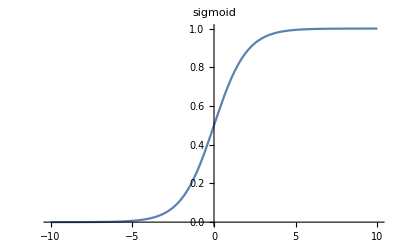

```mathematica
Plot[Sigmoid[x], {x, -10, 10}, PlotLabel->HoldForm[sigmoid]]
```

#### The Logit function

The Logit  is the inverse of the Logistic function σ(x), defined in (0,1) and yields values in (-∞, ∞).
Let’s find the inverse:
σ(x) = y =  1/(1+e^-x) ⇒  1+e^-x = 1/y  ⇒  e^-x = 1/y-1=(1-y)/y  ⇒  log(e^-x)=log((1-y)/y)  ⇒  -x = log((1-y)/y)  ⇒  x = log(y/(1-y)) = σ^-1(x)

```mathematica
Logit[x_]:= Log[x/(1-x)]
```

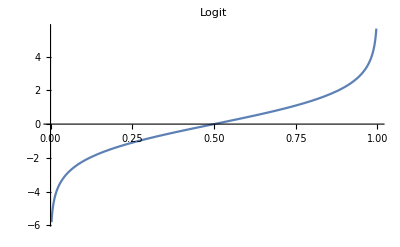

```mathematica
Plot[Logit[x], {x, 0, 1}, PlotLabel->HoldForm[Logit]]
```

### Range Adjuster

We define an Adjuster function which returns another function that maps a parameter in the range  (0,1) to the range  (low, high) of the original distribution.
We can use the Logistic function and its Logit inverse as follows:
Let
	h(t) = Logit(t) , t ∈ (0,1)
Than
	h^-1(d) = Sigmoid(d) , d ∈ (-∞, ∞)

```mathematica
Adjuster[low_, high_]:=With[{LOW=Sigmoid[low],HIGH=Sigmoid[high]}, Function[{t},Logit[LOW+t(HIGH-LOW)]]]
```

### Test Adjuster

For example, we can create an Adjuster for the range [2,5] and call it with values ∈ [0,1]

```mathematica
adj=Adjuster[2, 5];
Print[adj[0.01]];
```

2.01076

```mathematica
Print[adj[0.99]];
```

4.84348

Plot of the adjuster output in the range [0,1]

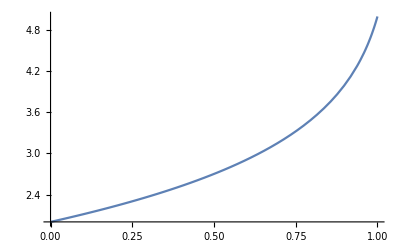

```mathematica
Print[Plot[adj[x], {x,0,1}]]
```

## Generate data

Arguments:

n: number of samples to generate

m: number of observations in each sample

f: the function to generate samples

ranges: an array [d X 2] of parameter ranges (e.g. for 2 parameters: [[0, 10], [0, ∞]])

bins: number of bins in histograms (default: max[samples]+1)

Returns:

a table of associations: histogram -> params (over all samples)

```mathematica
GenerateData[n_, m_, f_, ranges_, bins_:-1]:= 
Module[{nParams, adjusters, params,samples, nbins},

(*single parameter helper -> extract number out of list of length 1*)
Params[params_]:= If[Length[params]>1, params, params[[1]]];

(*number of parameters*)
nParams=Dimensions[ranges][[1]];

(*generate an adapter for each parameter range*)
adjusters=Table[Adjuster[ranges[[i,1]],ranges[[i,2]]],{i,1,nParams}];

(*generate N parameters cube in the range (0,1)*)
params=Table[adjusters[[j]][RandomReal[{0,1}]],{i,1,n},{j,1,nParams}];

(*output*)
(*generate N samples from the parameters*)
samples=Table[f[Params@params[[i]],m],{i,1,n}];

(*create a histogram from each sample*)
nbins=If [bins>0,bins,Max[samples]+1];
h[x_]:=HistogramList[x, {0,nbins,1}][[2]];

(*output*)
Table[h@samples[[i]]->Params@ params[[i]], {i, 1, n}]
]
```

Test GenerateData

```mathematica
YuleSimon[{α_,β_}, m_]:=RandomVariate[WaringYuleDistribution[α,β],m];
YuleSimonRanges = {{2,3},{0,10}};

Print[];
Print["YuleSimon"];
YuleSimonData = GenerateData[5,10,YuleSimon, YuleSimonRanges];
Print[YuleSimonData//TableForm];
```

YuleSimon

{10,0,0,0,0,0}→{2.93274,0.219345}
{10,0,0,0,0,0}→{2.06407,0.0617528}
{10,0,0,0,0,0}→{2.67975,0.0397917}
{5,0,1,3,0,1}→{2.04591,1.58077}
{6,1,3,0,0,0}→{2.58062,3.35483}

## DNN

```mathematica
CreateNet[bins_, nParams_]:=( 
NetChain[{
LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 
(*DropoutLayer[0.1],*)
LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 
(*DropoutLayer[0.1],*)
LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 
DropoutLayer[0.1],
LinearLayer[nParams]},
"Input"->bins, 
"Output" -> If[nParams>1,nParams,"Scalar"]]
)
```

### Test DNN

NetGraph[<>]

{2.1,0.5}

Evaluate params:{2.1,0.5}

Predicted:{2.59548,0.475408}

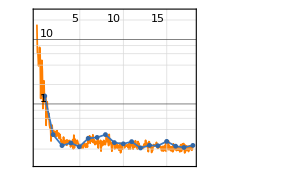
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:288  rounds:18  time:14s  examples/s:1402
data | ,,  training examples:1000  validation examples:250  processed examples:18432  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.09×10^-1
validation | ,,  loss:2.28×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
m = 256;
n = 1000;

(*generate data*)
trainSet=GenerateData[n,m,YuleSimon, YuleSimonRanges];
bins = Length@trainSet[[1]][[1]];
valSet=GenerateData[n/4,m,YuleSimon, YuleSimonRanges, bins];

(*train*)
nParams=Dimensions[YuleSimonRanges][[1]];
net = NetInitialize@CreateNet[bins, nParams];
Print[NetGraph[net]];
results=NetTrain[net,
trainSet,
All, Method->"ADAM", 
ValidationSet->valSet, 
LossFunction->MeanAbsoluteLossLayer[]];

(*evaluate*)
params={2.1,0.5}
Print["Evaluate params:", params];
trained = results["TrainedNet"];
predicted = trained[HistogramList[YuleSimon[params,m],{0,bins,1}][[2]]];
Print["Predicted:", predicted];

(*Plot NetTrain Results*)
Print[results];
```

## Experiments

Define some longtail distributions.
Run an experiment for each longtail distribution.

Assuming 2 parameters for the distribution:

Generate learning samples (train/val) for the given parameters ranges (using GenerateData defined above).

Train a NN model for predicting the parameters corresponding to each sample.

Create a 2-dimensional parameters mesh on the unit square, with 0.1 resolution (i.e: 0.1, 0.2, ... , 0.9)
The mesh is a cube of size 9^2 (81 cell matrix), each containing pair of parameter values (t_1,t_2) ∈ [0.1,...,0.9]

At each mesh point:

Run several trials. At each trial:

Create test data (a histogram of a sample generated at that mesh point)

Predict the parameters at the mesh point, averaging the prediction error.

Compute the Cramer-Raw bound for the mesh point.

Record the relation  (prediction error)/(Cramer-Raw bound)

Plot a surface of the relation above at each mesh point, hopefully showing a value around 2 at each point.

#### Define longtail distributions

```mathematica
(*Sample from Poisson distribution with mean μ *)
PoissonRV[μ_, m_]:=RandomVariate[PoissonDistribution[μ],m]

(*Sample m observations from the Yule distribution with shape parameters α and β.*)
YuleSimonRV[{α_,β_}, m_]:=RandomVariate[WaringYuleDistribution[α,β],m]

(*Sample m observations from the PowerLaw distribution with domain parameter k and shape parameter a.*)
PowerLawRV[{k_,a_}, m_]:=RandomVariate[PowerDistribution[k,a],m]

(*Log-Normal*)
LogNormalRV[{μ_,σ_}, m_]:=RandomVariate[LogNormalDistribution[μ,σ],m]
```

#### Define an Association for each distribution

```mathematica
m =256;
distributions = Association[
"poisson" -> Association["dist"->PoissonRV, "ranges"->{{0,10}}, "m"->m],
"yulesimon" -> Association["dist"->YuleSimonRV, "ranges"->{{2,3},{0,10}}, "m"->m],
"powerlaw" -> Association["dist"->PowerLawRV, "ranges"->{{1,10},{0,10}}, "m"->m],
"lognormal" -> Association["dist"->LogNormalRV, "ranges"->{{1,2},{0,1}}, "m"->m]
];
```

### Run the experiments

An experiment for a single distribution

```mathematica
RunExperiment[distributions_, distname_]:=
Module[{dist, f, ranges, n, m, model, bins},
(*Get definitions for the distribution specified by distname*)
dist = distributions[distname];
f = dist["dist"];
ranges = dist["ranges"];
n = 1000;
m = dist["m"];

(*Train the network*)
{model, bins} = TrainNet[f, ranges, n, m];

(*Evaluate*)
EvaluateModel[model, ranges, m, bins]
]

TrainNet[f_, ranges_, n_, m_]:=Module[{ trainSet, bins, valSet, nParams, net, model},
(*Generate learning samples (train/val) for the parameters ranges (using GenerateData defined above).*)
trainSet=GenerateData[n,m,f, ranges];
(*we need the same number of bins for the validation set*)
bins = Length@trainSet[[1]][[1]];
valSet=GenerateData[n/4,m,f, ranges, bins];

(*Train a NN model for predicting the parameters corresponding to each sample.*)
nParams=Dimensions[ranges][[1]];
net = NetInitialize@CreateNet[bins, nParams];

model=NetTrain[
net,trainSet,
All,
Method->"ADAM", 
ValidationSet->valSet, 
LossFunction->MeanAbsoluteLossLayer[]];

(*output model & input size*)
{model, bins}
]

EvaluateModel[model_, ranges_, m_, bins_]:=Module[{adjuster1, adjuster2, mesh},

(*Create an adjuster for each parameter*)
adjuster1=Adjuster[ranges[[1,1]],ranges[[1,2]]];
adjuster2=Adjuster[ranges[[2,1]],ranges[[2,2]]];

(*Create a 2-dimensional parameters mesh on the unit square*)
mesh = Table[{adjuster1[i],adjuster2[j]},{i,0.1,0.9,0.1 },{j,0.1,0.9,0.1 }];

(*output*)
(*Process each mesh point*)
Table[EvaluateMeshPoint[model, f, mesh[[i,j]], m, bins],{i,1,9 },{j,1,9 }]
]

EvaluateMeshPoint[model_, f_, params_, m_, bins_]:= 
Module[{sample, histogram, cycles, predicted, error},
(*Run 3 cycles*)
error=0;
cycles=3;
For[i=0; , i < cycles, i+=1,
(*Create a histogram from a sample generated using the given parameters)*)
sample=f[params,m];
histogram = HistogramList[sample, {0,bins,1}][[2]];

(*Predict the parameters, averaging the prediction absolute error.*)
predicted = model[histogram];
error += Abs[predicted - params];
];

(*avg the errors across all parameters*)
error=Mean[error /cycles];

(*Compute the Cramer-Raw bound for the mesh point.*)
(*Return the relation*)
error/CramerRawBound[params, m]
]

(*lilo:TODO*)
CramerRawBound[params_, m_]:=0.2
```

```mathematica
(*RunExperiment[distributions, "yulesimon"]*)
(*dist = distributions["poisson"];*)
dist = distributions["yulesimon"];
(*dist = distributions["powerlaw"];*)
(*dist = distributions["lognormal"];*)
f = dist["dist"];
ranges = dist["ranges"];
n = 1000;
m = dist["m"];
{model, bins} = TrainNet[f, ranges, n, m];
```

```mathematica
trained = model["TrainedNet"];
EvaluateModel[trained, ranges, m, bins]
```

{{0.76259,0.573473,0.58498,0.975106,0.422654,0.823161,0.963579,0.648348,1.36691},{0.596522,0.802001,0.446859,0.649917,1.05843,0.785025,0.538128,0.385428,0.949448},{0.372663,0.626205,0.675076,0.440785,0.602737,0.599903,0.994268,0.757448,1.09219},{0.278193,0.497807,0.424108,0.633882,0.651407,1.20169,0.34958,0.727599,1.11657},{0.226971,0.748732,0.35109,0.855125,0.983723,0.844684,0.881901,0.445312,2.08892},{0.492291,0.511542,0.70297,0.655886,0.803975,0.897008,1.14235,1.03656,0.909245},{0.695147,0.645791,0.534108,0.612848,0.736411,0.957493,1.01206,0.92958,0.771213},{1.02423,0.593042,0.640921,0.908302,0.626141,1.14456,1.11128,0.909585,0.916605},{1.31801,0.383064,0.431623,0.693542,0.589943,0.762084,0.629382,0.622206,0.202178}}

Fisher Information

```mathematica
(*𝕀(θ) = Var(∂/(∂θ)log (f(θ|y)))*)
```

```mathematica
(*single parameter distribution*)
FI[dist_]:= (
f=PDF[dist[α],x]; 
h=D[Log[f],{α,2}];
(fim=Expectation[-h,x\[Distributed]dist[α]])
)

(*two parameters distribution*)
FIM[dist_]:= (
f=PDF[dist[α,β],x]; 
h=D[Log[f],{{α,β},2}];
(fim=Expectation[-h,x\[Distributed]dist[α,β]])//MatrixForm
)
```

### Examples

```mathematica
FI@PoissonDistribution
```

1/α

```mathematica
FIM@NormalDistribution
```

(1/β^2 | 0
0 | 2/β^2)

```mathematica
FIM@LogNormalDistribution
```

(1/β^2 | 0
0 | 2/β^2)

```mathematica
FIM@PowerDistribution
```

(β/α^2 | -1/α
-1/α | 1/β^2)

```mathematica
(*FI@WaringYuleDistribution*)
(*FIM@WaringYuleDistribution*)
```